```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(κ+k)/γ,κ/γ},{κ/γ,-κ/γ}}
```

{{(-k-κ)/γ,κ/γ},{κ/γ,-κ/γ}}

```mathematica
MatrixForm[M]
```

((-k-κ)/γ | κ/γ
κ/γ | -κ/γ)

```mathematica
expM=MatrixExp[M*(-tp)]
```

{{-(ⅇ^((tp (k γ+2 γ κ-γ √(k^2+4 κ^2)))/(2 γ^2)) (k γ-γ √(k^2+4 κ^2)))/(2 γ √(k^2+4 κ^2))+(ⅇ^((tp (k γ+2 γ κ+γ √(k^2+4 κ^2)))/(2 γ^2)) (k γ+γ √(k^2+4 κ^2)))/(2 γ √(k^2+4 κ^2)),(ⅇ^((tp (k γ+2 γ κ-γ √(k^2+4 κ^2)))/(2 γ^2)) κ)/(√(k^2+4 κ^2))-(ⅇ^((tp (k γ+2 γ κ+γ √(k^2+4 κ^2)))/(2 γ^2)) κ)/(√(k^2+4 κ^2))},{(ⅇ^((tp (k γ+2 γ κ-γ √(k^2+4 κ^2)))/(2 γ^2)) κ)/(√(k^2+4 κ^2))-(ⅇ^((tp (k γ+2 γ κ+γ √(k^2+4 κ^2)))/(2 γ^2)) κ)/(√(k^2+4 κ^2)),-(ⅇ^((tp (k γ+2 γ κ-γ √(k^2+4 κ^2)))/(2 γ^2)) (-k γ-γ √(k^2+4 κ^2)))/(2 γ √(k^2+4 κ^2))+(ⅇ^((tp (k γ+2 γ κ+γ √(k^2+4 κ^2)))/(2 γ^2)) (-k γ+γ √(k^2+4 κ^2)))/(2 γ √(k^2+4 κ^2))}}

```mathematica
covar=Integrate[expM.{{2*Subscript[T, c]/γ,0},{0,2*Subscript[T, h]/γ}}.Transpose[expM],{tp,-Infinity,0},Assumptions->{γ>0,k>0,κ>0}]
```

{{((k+κ) T_c+κ T_h)/(k (k+2 κ)),(κ T_c+(k+κ) T_h)/(k (k+2 κ))},{(κ T_c+(k+κ) T_h)/(k (k+2 κ)),(κ^2 T_c+(k^2+3 k κ+κ^2) T_h)/(k κ (k+2 κ))}}

```mathematica
FullSimplify[covar/.{Subscript[T, c]->Subscript[T, h]},Assumptions->{γ>0,k>0,κ>0}]
```

{{T_h/k,T_h/k},{T_h/k,((k+κ) T_h)/(k κ)}}

```mathematica
P[x_,y_,kk_]:=Simplify[Exp[-1/2*{x,y}.Inverse[covar].{x,y}]]/.{k->kk}
```

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2
```

(2 U_0)/L^2

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2
```

(2 U_0)/l^2

```mathematica
SubMinus[f]=FullSimplify[Integrate[P[x,y,SubMinus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

ⅇ^(-(2 x^2 U_0 (L^2 κ+U_0))/(L^4 κ (T_c+T_h)+2 L^2 T_c U_0)) √π √((L^4 κ^2 (T_c+T_h)^2+8 L^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (L^2 κ+U_0) (L^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
SubPlus[f]=FullSimplify[Integrate[P[x,y,SubPlus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

ⅇ^(-(2 x^2 U_0 (l^2 κ+U_0))/(l^4 κ (T_c+T_h)+2 l^2 T_c U_0)) √π √((l^4 κ^2 (T_c+T_h)^2+8 l^2 κ T_c T_h U_0+4 T_c T_h U_0^2)/(κ (l^2 κ+U_0) (l^2 κ (T_c+T_h)+2 T_c U_0)))

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{x->0})==SubPlus[A]*(SubPlus[f]/.{x->0})&&SubMinus[A]*Integrate[SubMinus[f],{x,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]+SubPlus[A]*Integrate[SubPlus[f],{x,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{A_-→(2 √2 U_0 (L^2 κ+U_0) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))))/(l L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0))))),A_+→(2 √2 U_0 (l^2 κ+U_0) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))))/(l L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0)))))}}

## Current

```mathematica
Subscript[J, R] = Simplify[-(k*x+κ*(x-y))/γ*P[x,y,k]-Subscript[T, c]/γ*D[P[x,y,k],x],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

-(ⅇ^(-((k+2 κ) (κ (k y^2+(x-y)^2 κ) T_c+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) T_h))/(2 (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))) κ^2 (T_c-T_h) ((k y+(-x+y) κ) T_c-(k x+(x-y) κ) T_h))/(γ (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->l,k->SubPlus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{y→(l^3 κ (T_c+T_h)+2 l T_h U_0)/(l^2 κ (T_c+T_h)+2 T_c U_0)}}

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->-L,k->SubMinus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{y→-(L^3 κ (T_c+T_h)+2 L T_h U_0)/(L^2 κ (T_c+T_h)+2 T_c U_0)}}

```mathematica
Subscript[J, right]=Simplify[Integrate[SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]},{y,y/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, left]=Simplify[Integrate[SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]},{y,-Infinity,y/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, total]= Simplify[Subscript[J, right]+Subscript[J, left],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, paper] =Subscript[J, total]/.{Subscript[T, c]->0.1,Subscript[T, h]->T,Subscript[U, 0]->1,κ->1,l->9,L->1,γ->0.1};
```

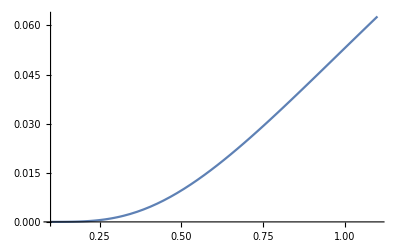

```mathematica
Plot[Subscript[J, paper],{T,0.1,1.1}]
```

```mathematica
a = Import["/home/ieshghi/Documents/code/dumbbell/data/decoupled_hot/sl_lowt.csv","Table"];
```

```mathematica
tvals = Import["/home/ieshghi/Documents/code/dumbbell/data/decoupled_hot/tvals.csv","Table"];
```

```mathematica
tvals=Flatten[tvals,1];
```

```mathematica
a  = Flatten[a,1];
```

```mathematica
data = Transpose@{tvals,a};
```

```mathematica
plt1 = ListPlot[data];
plt2 = Plot[Subscript[J, paper],{T,0.1,1.1},PlotStyle->{Orange}];
```

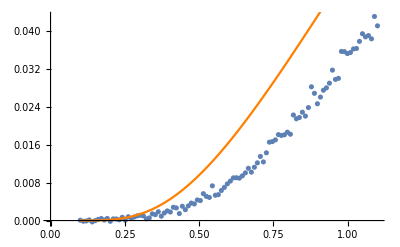

```mathematica
Show[plt1,plt2]
```

```mathematica
stiffspr = Series[Subscript[J, total],{κ,∞,0}]
```

$Aborted